The role of edible habitat complexity in food webs (P3)

Eden Forbes, 2025 - 2026

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"C:\Users\eforb\OneDrive\Desktop\RESEARCH\CODEBASE\Dynamica\Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Building Block Visualizers

```mathematica
T2[x_]:=(595/(30+ x));
```

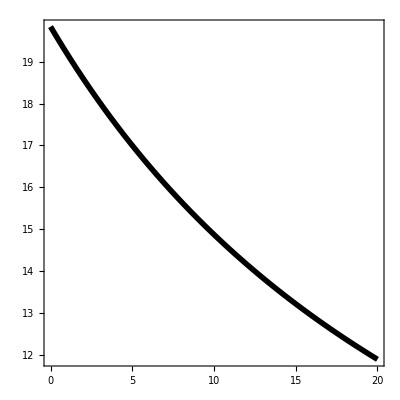

```mathematica
Plot[T2[x],{x,0,20},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,All},Frame->True,LabelStyle->{Black,20},AspectRatio->1
]
```

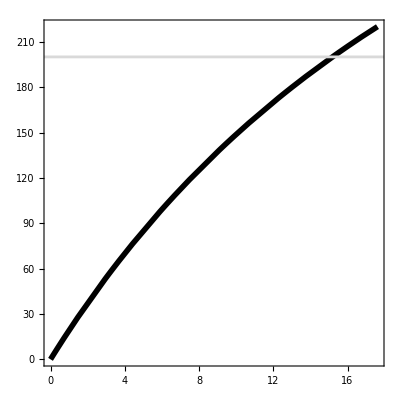

```mathematica
Plot[T2[x]*x,{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,220}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
β[rat_,steep_]:= (rat)^steep/((rat)^steep+α^steep); (* When the ratio is 10:1 (1),  start eating Dreissena *)
```

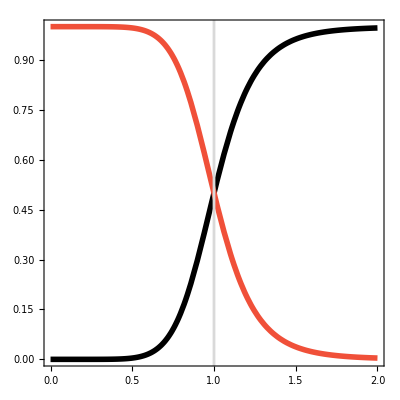

```mathematica
Show[
Plot[β[x,8]/.{α->1},{x,0,2},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
(*Plot[β[x,1]/.{α->1},{x,0,2},PlotStyle->{Black,Dashed,Thickness[0.01]},PlotRange->All],*)
Plot[1-β[x,8]/.{α->1},{x,0,2},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},PlotRange->All],
(*Plot[1-β[x,1]/.{α->1},{x,0,2},PlotStyle->{Blue,Dashed,Thickness[0.01]},PlotRange->All],*)
Frame->True,LabelStyle->{Black,20},AspectRatio->1,AxesOrigin->{0,0},GridLines->{{1},{}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
T2B[x_]:=((595 β[1,4])/(30+ x β[1,4]));
```

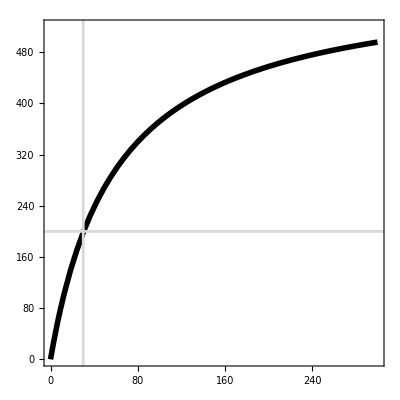

```mathematica
Plot[T2B[x]*x/.{α->1},{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,520}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]]
```

## EHC

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
EDIB = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V,
(((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ,
b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,100000},{P,-0.01,100000}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,1},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0.06,0.12},{hvp,0,1},{fvp,0,1},{fjp,0,1},{dp,0.0001,0.008},{yp,0,10000},{yj,0,10000},
{α,0.0001,1},{ω,1,4},{δ,1,3},
{b,0.0001,2000},{g,0.0001,1000},{kz,1,1000},{kv,100,100000000},{dj,0.0001,1},{dm,0.0001,1}
}]
EDIB = EDIB/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.09,hvp-> 30, fvp->0.08*4900/0.67,fjp->0.08*4900/1,dp->0.004,yj->1, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,fjp,dp,yp,yj,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,yj,fjp,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V;
dP = (((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ;
dJ =b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J;
dM = g J (1-M/kz)- dm M;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)+(fvp P (V/M)^ω (-hvp (V/M)^ω-(hvp+J) α^ω (1+ω)))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fvp V (V/M)^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | (fvp P V (V/M)^ω α^ω)/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (V (M r (V/M)^(2 ω) (hvp+V)^2 δ+(hvp+J)^2 M r α^(2 ω) δ+(hvp+J) (V/M)^ω α^ω (2 M r (hvp+V) δ+fvp kz P ω)))/(kz M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(ep P (V/M)^ω (-fjp J yj α^ω (V+(hvp+V) ω)+fvp V yv (hvp (V/M)^ω+(hvp+J) α^ω (1+ω))))/(V yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -dp+(ep (fvp V (V/M)^ω yv+fjp J yj α^ω))/((V/M)^ω (hvp+V) yp+(hvp+J) yp α^ω) | (ep P α^ω ((V/M)^ω (fjp (hvp+V) yj-fvp V yv)+fjp hvp yj α^ω))/(yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (ep P (V/M)^ω (fjp J (hvp+V) yj-fvp (hvp+J) V yv) α^ω ω)/(M yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(fjp J P (V/M)^ω α^ω (V+(hvp+V) ω))/(V ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fjp J α^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | -dj-g-(b M)/kz-(fjp P α^ω ((V/M)^ω (hvp+V)+hvp α^ω))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | b-(b J)/kz-(fjp J P (V/M)^ω (hvp+V) α^ω ω)/(M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,jVJ,jVM},{jPV,jPP,jPJ,jPM},{jJV,jJP,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | jVJ | jVM
jPV | jPP | jPJ | jPM
jJV | jJP | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV+jJP jMM jPJ x-jJP jMJ jPM x+jJM jMJ jPP x-jJJ jMM jPP x+jJV jMM jVJ x+jJV jPP jVJ x-jJP jPV jVJ x-jJV jMJ jVM x-jJV jPJ jVP x+jJJ jPV jVP x+jMM jPV jVP x+jJM jMJ jVV x-jJJ jMM jVV x+jJP jPJ jVV x-jJJ jPP jVV x-jMM jPP jVV x-jJM jMJ x^2+jJJ jMM x^2-jJP jPJ x^2+jJJ jPP x^2+jMM jPP x^2-jJV jVJ x^2-jPV jVP x^2+jJJ jVV x^2+jMM jVV x^2+jPP jVV x^2-jJJ x^3-jMM x^3-jPP x^3-jVV x^3+x^4

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J34*J43-J44*J33)+(-J11*J44)+(J13 J31-J11*J33)+(-J22*J44)+(J23 J32-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J23 J32 J44 -J32 J43 J24 +J34 J43 J22 -J33 J44 J22 +J31 J13 J44 +J31 J13 J22 -J32 J21 J13 - J31 J43 J14 -J31 J23 J12+ J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 +J32 J23 J11- J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(- J31 J44 J22 J13 + J32 J44 J21 J13 + J32 J43 J22 J14 - J32 J43 J21 J14 +J31 J44 J23 J12 -J31 J43 J24 J12 +
J34 J43 J12 J21-J33 J44 J12 J21-J32 J44 J23 J11 +J32 J43 J24 J11 - J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - kz

```mathematica
Clear[kz]
```

```mathematica
solsKZ= Solve[{(dV/.{P->0})==0,(dJ/.{P->0})==0, (dM/.{P->0})==0},{V,J,M}];
```

```mathematica
solsKZ
```

{{V→0,J→0,M→0},{V→0,J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→(-dj dm kz+b g kz-dm g kz)/(b (dm+g))},{V→(-dv kv+kv r)/r,J→0,M→0},{V→(kv (-b dm dv-b dv g+b dm r+b g r-dj dm r δ+b g r δ-dm g r δ))/(b (dm+g) r),J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→((-dj dm+b g-dm g) kz)/(b (dm+g))}}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,2,2]]];
Mp = Re[solsKZ[[4,3,2]]];

P0=(((((yv ep)/yp)fvp β[Vp,Mp]Vp)+(((yj ep)/yp)(1-β[Vp,Mp])fjp Jp))/(hvp+β[Vp,Mp] Vp + (1-β[Vp,Mp]) Jp))/dp;
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

```mathematica
min = 50; max = 3000; gran = 20;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->i*gran},{{3107.66,0.008,500,500}},3000,MaxSteps->100000, PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = FindPeaks[$Trajectories[[1]][[All,1]], InterpolationOrder->3,Padding->6][[All,2]];
vvalleys = (FindPeaks[$Trajectories[[1]][[All,1]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
ppeaks = FindPeaks[$Trajectories[[1]][[All,2]], InterpolationOrder->3,Padding->6][[All,2]];
pvalleys = (FindPeaks[$Trajectories[[1]][[All,2]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
jpeaks = FindPeaks[$Trajectories[[1]][[All,3]], InterpolationOrder->3,Padding->6][[All,2]];
jvalleys = (FindPeaks[$Trajectories[[1]][[All,3]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
mpeaks = FindPeaks[$Trajectories[[1]][[All,4]], InterpolationOrder->3,Padding->6][[All,2]];
mvalleys = (FindPeaks[$Trajectories[[1]][[All,4]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;

For[j=1,j<=Length[vpeaks],j++,
AppendTo[Vpeaks,{i*gran,vpeaks[[j]]}]
];
For[j=1,j<=Length[vvalleys],j++,
AppendTo[Vvalleys,{i*gran,vvalleys[[j]]}]
];

For[j=1,j<=Length[ppeaks],j++,
AppendTo[Ppeaks,{i*gran,ppeaks[[j]]}]
];
For[j=1,j<=Length[pvalleys],j++,
AppendTo[Pvalleys,{i*gran,pvalleys[[j]]}]
];

For[j=1,j<=Length[jpeaks],j++,
AppendTo[Jpeaks,{i*gran,jpeaks[[j]]}]
];
For[j=1,j<=Length[jvalleys],j++,
AppendTo[Jvalleys,{i*gran,jvalleys[[j]]}]
];

For[j=1,j<=Length[mpeaks],j++,
AppendTo[Mpeaks,{i*gran,mpeaks[[j]]}]
];
For[j=1,j<=Length[mvalleys],j++,
AppendTo[Mvalleys,{i*gran,mvalleys[[j]]}]
];


vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

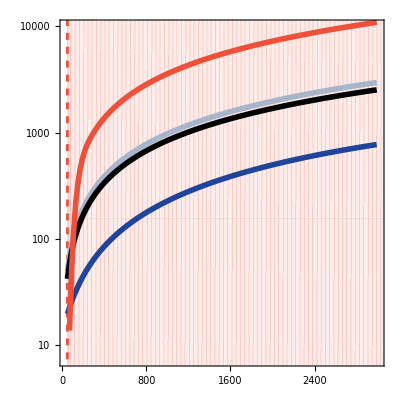

```mathematica
Show[
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[4000>x>50,{x,0,4000},{y,-100,2500}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.0639 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
RegionPlot[0.064 > x>-1,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->None],*)
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],

(*ListLogPlot[Jvalleys,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Dashed}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],*)
ListLogPlot[Jpeaks, Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01] }],

(*ListLogPlot[Mvalleys,Joined->True, PlotStyle->{Black,Dashed}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],*)
ListLogPlot[Mpeaks, Joined->True, PlotStyle->{Black,Thickness[0.01] }],

(*ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],*)
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01] }],

(*ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],*)
ListLogPlot[Ppeaks, Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01] }],

Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{38.73,3000},{2,9.2}}]
```

### CHART - alpha

#### MIN MAX MEAN (Pop EQ)

```mathematica
Clear[α];
```

```mathematica
min = 0.005; max =0.5; gran = 0.005;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{{0.8006464079570448,48.85631664928134,39.201988939270194,40.45732780780099}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

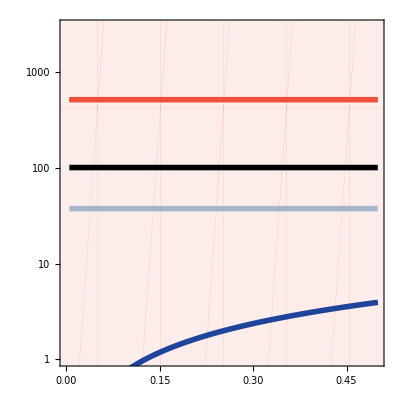

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.425 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],*)
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,0.5},{0,8}}]
```

#### Loops

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kz=200;kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; ω=4; δ=2;
```

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j12s,J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j13s,J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j14s,J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j21s,J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j22s,J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j23s,J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j24s,J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j31s,J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j32s,J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j33s,J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j34s,J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j43s,J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j44s,J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

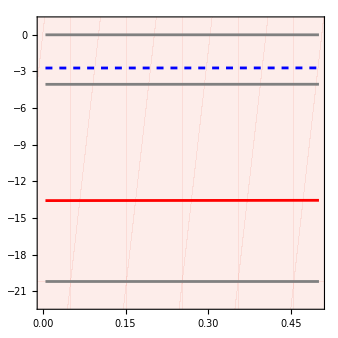

```mathematica
(* All Levels *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L2s*0.01}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],L1s*0.01}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],OCs}],PlotStyle->{Blue,Dashed}],
PlotRange->{{0,0.5},{-22,1}}, LabelStyle->{Black,16},AspectRatio->1
]
```

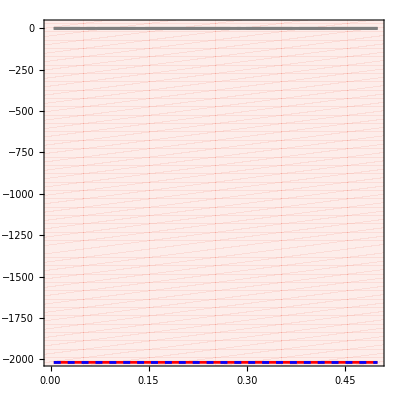

```mathematica
(* F1 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],(j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s)}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],(j22s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(j11s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],L1s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-2000,10}}, LabelStyle->{Black,16},AspectRatio->1
]
```

```mathematica
ListLinePlot[Transpose[{Range[min,max,gran],(j44s)}],PlotStyle->Gray]
ListLinePlot[Transpose[{Range[min,max,gran],(j33s)}],PlotStyle->Red]
ListLinePlot[Transpose[{Range[min,max,gran],(j22s)}],PlotStyle->Gray]

ListLinePlot[Transpose[{Range[min,max,gran],(j11s)}],PlotStyle->Gray]
```

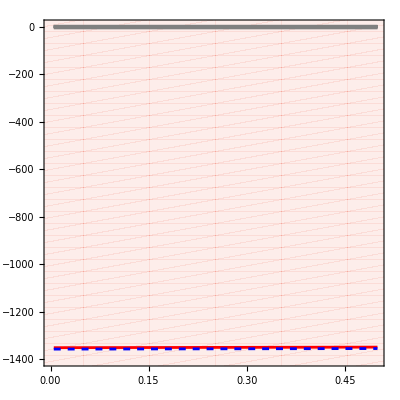

```mathematica
(* F2 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j23s j32s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j12s*j21s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s*j43s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j44s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j33s)}],PlotStyle->Red],

ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-1400,0}}, LabelStyle->{Black,16},AspectRatio->1
]
```

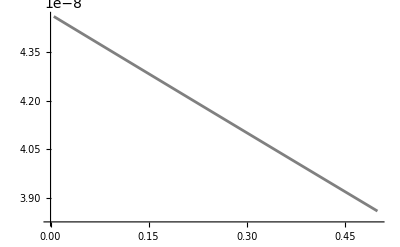

```mathematica
ListLinePlot[Transpose[{Range[min,max,gran],(j12s*j21s)}],PlotStyle->Gray]
```

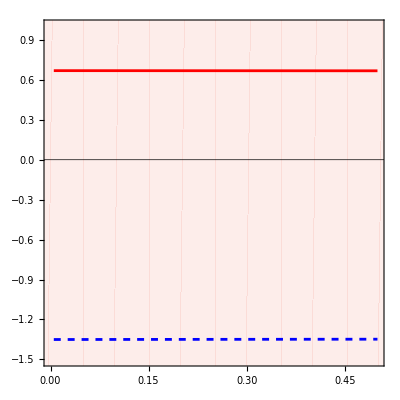

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],-j11s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],j33s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j33s)*0.001}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-1.5,1}}, LabelStyle->{Black,16},AspectRatio->1,
GridLines->{{}, {0}},GridLinesStyle->Black
]
```

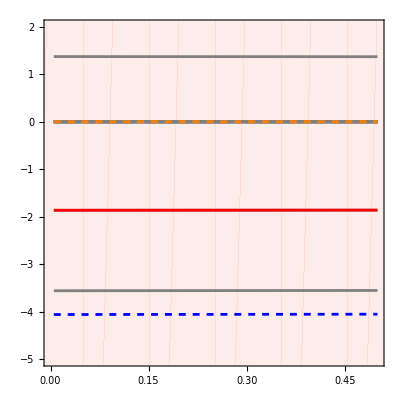

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],(j31s j43s j14s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j31s j23s j12s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j44s j21s j12s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j11s)}],PlotStyle->Gray], (* Green *)
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j11s)}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j23s j11s)}],PlotStyle->Gray], (* Blue *)
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j21s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j13s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j13s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j43s j24s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j23s j32s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j22s j11s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j44s j33s j11s)}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],(-j33s j21s j12s )}],PlotStyle->{Orange, Dashed}],


ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-5,2}}, LabelStyle->{Black,16},AspectRatio->1
]
```

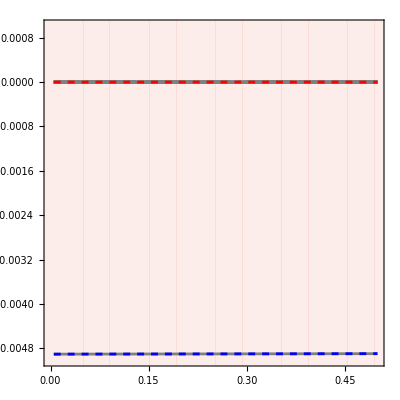

```mathematica
(* F4 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],(j31s j44s j22s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j44s j21s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j43s j22s j14s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j43s j21s j14s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j44s j23s j12s)}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(j31s j43s j24s j12s )}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j12s j21s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j44s j23s j11s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j43s j24s j11s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s j43s j22s j11s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s j22s j33s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j12s j21s)}],PlotStyle->{Red,Dashed}],


ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,0.5},{-0.005,0.001}}, LabelStyle->{Black,16},AspectRatio->1
]
```

### CHART - omega

#### MIN MAX MEAN (Pop EQ)

```mathematica
Clear[ω, kz];
min = 1; max =3; gran = 0.1;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},3000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

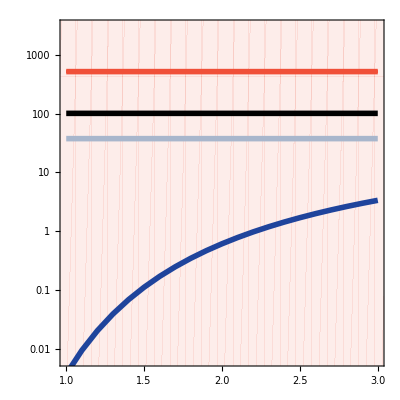

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],

Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,3},{-5,8}},AxesOrigin->{0.01,-5}]
```

#### Loops

```mathematica
Clear[ω]
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kz=200;kv=1000; dv=1/30; yv=0.67; ep=0.09; hvp= 30; fvp=0.08*4900/0.67; dp=0.004; yp=4900;yj = 1; fjp = 0.08*4900; α=1; δ=2;
```

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j12s,J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j13s,J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j14s,J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j21s,J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j22s,J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j23s,J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j24s,J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j31s,J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j32s,J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j33s,J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j34s,J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j43s,J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
AppendTo[j44s,J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

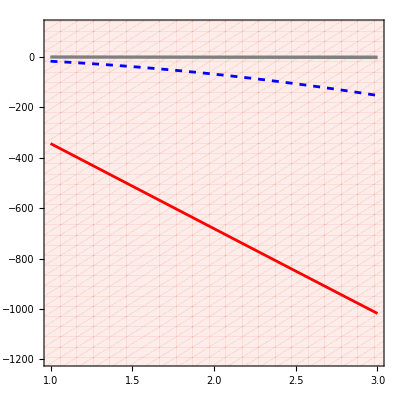

```mathematica
(* All Levels *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],L1s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],OCs*100}],PlotStyle->{Blue,Dashed}],
PlotRange->{{1,3},{-1200,120}},Frame->True, LabelStyle->{Black,16},AspectRatio->1
]
```

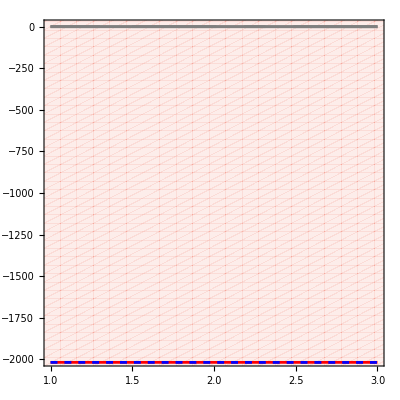

```mathematica
(* F1 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],(j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s)}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],(j22s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(j11s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],L1s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-2000,0}}, LabelStyle->{Black,16},AspectRatio->1
]
```

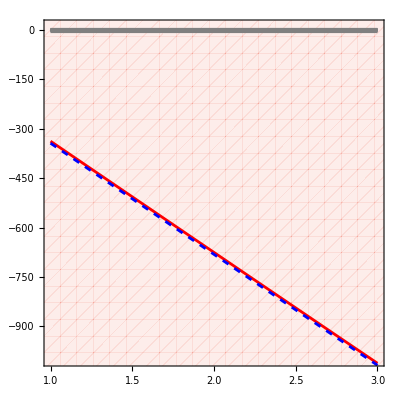

```mathematica
(* F2 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j23s j32s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j22s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j12s*j21s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s*j43s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j44s*j33s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s)}],PlotStyle->Gray],

ListLinePlot[Transpose[{Range[min,max,gran],(-j11s*j33s)}],PlotStyle->Red],

ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-1000,10}}, LabelStyle->{Black,16},AspectRatio->1
]
```

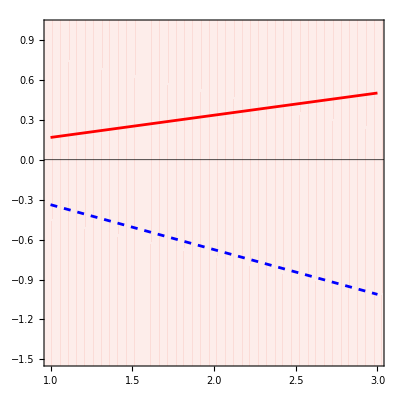

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],-j11s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],j33s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)*0.001}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-1.5,1}}, LabelStyle->{Black,16},AspectRatio->1,GridLines->{{0}, {0}},GridLinesStyle->Black
]
```

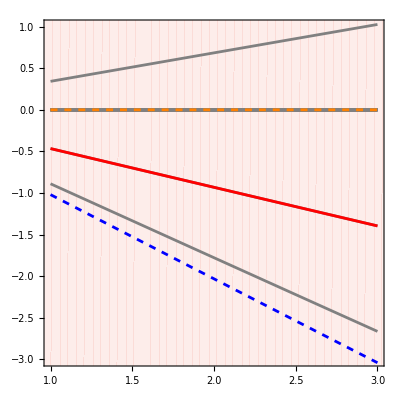

```mathematica
(* F3 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],(j31s j43s j14s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j31s j23s j12s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j44s j21s j12s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j11s)}],PlotStyle->Gray], (* Green *)
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j11s)}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j23s j11s)}],PlotStyle->Gray], (* Blue *)
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j21s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j13s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j13s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j22s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j43s j24s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j23s j32s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j22s j11s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j44s j33s j11s)}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],(-j33s j21s j12s )}],PlotStyle->{Orange, Dashed}],


ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{1,3},{-3,1}}, LabelStyle->{Black,16},AspectRatio->1
]
```

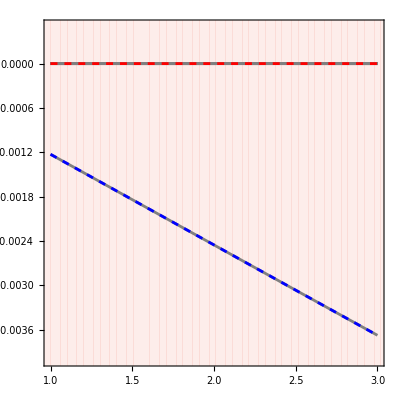

```mathematica
(* F4 *)
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-3000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],(j31s j44s j22s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j44s j21s j13s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j43s j22s j14s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j43s j21s j14s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j31s j44s j23s j12s)}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(j31s j43s j24s j12s )}],PlotStyle->Gray], 
ListLinePlot[Transpose[{Range[min,max,gran],(-j34s j43s j12s j21s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j32s j44s j23s j11s )}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j32s j43s j24s j11s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j34s j43s j22s j11s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(-j11s j22s j33s j44s)}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j33s j44s j12s j21s)}],PlotStyle->{Red,Dashed}],


ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->{Blue,Dashed}],


PlotRange->{{1,3},{-0.004,0.0005}}, LabelStyle->{Black,16},AspectRatio->1
]
```

### CHART - bj & dj

```mathematica
LH2[b0_,dj0_]:=
Module[{bj=b0, djj = dj0},
(* Equilibrate *)
DisplayTrajectories[EDIB/.{g->bj,dj->djj,α->0.15},{{241.044,0.121,199.998,168.785}},100000];
(* R0 *)
DisplayTrajectories[EDIB/.{g->bj,dj->djj, α->0.15},{Last[First[$Trajectories]]},1000, MaxIterations->Infinity,MaxSteps->Infinity,MaxStepSize->0.1];
subs = First[$Trajectories][[-50 ;; -1]][[All,1]];
out = Max[subs]-Min[subs];
{out, Max[subs]}
]
```

```mathematica
granb = 20; (* 0.025 *)
grandj = 0.0001; (* 0.0005 *)
startb = 1000;
startdj = 1/730;
maxb = 1500;
maxdj = 1/182; (* 0.115 *)
lifehist2 = {};
```

```mathematica
For[i=(startb/granb),i<=(maxb/granb),i++,
Clear[bin];
bin = i * granb;
For[j=(startdj/grandj),j<=(maxdj/grandj),j++,
Clear[djin];
djin = j * grandj;
AppendTo[lifehist2,{bin, djin,LH2[bin,djin]}];
]
]
```

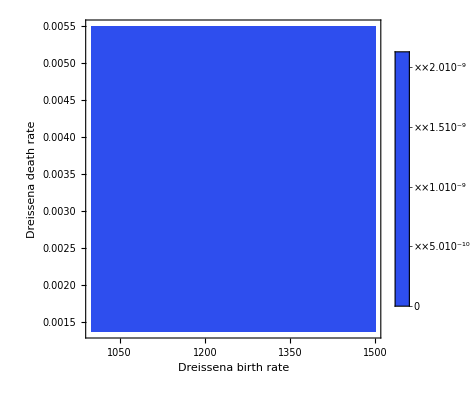

```mathematica
(* Max - Min I density (stability)*)
ListDensityPlot[ArrayReshape[lifehist2[[All,3]][[All,1]],{IntegerPart[(maxb/granb) - (startb/granb)+1],IntegerPart[(maxdj/grandj)-(startdj/grandj)+1]}],DataRange->{{startb,maxb},{startdj,maxdj}},ColorFunction->(ColorData["TemperatureMap",#/1.0]&),ColorFunctionScaling->False,
PlotLegends->Automatic, PlotRange->All,
FrameLabel->{"Dreissena birth rate", "Dreissena death rate"},LabelStyle->{Black,16}]
```

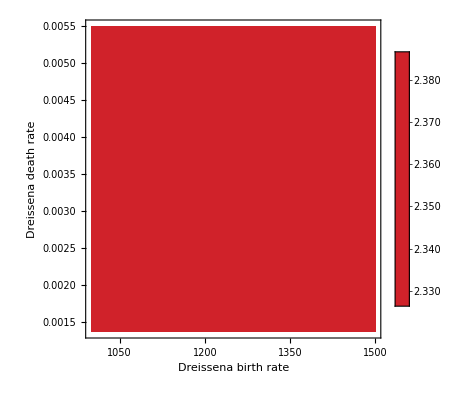

```mathematica
(* Maximum I density*)
ListDensityPlot[ArrayReshape[lifehist2[[All,3]][[All,2]],{IntegerPart[(maxb/granb) - (startb/granb)+1],IntegerPart[(maxdj/grandj)-(startdj/grandj)+1]}],DataRange->{{startb,maxb},{startdj,maxdj}},ColorFunction->(ColorData["TemperatureMap",#/2.3]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->Automatic,
FrameLabel->{"Dreissena birth rate", "Dreissena death rate"},LabelStyle->{Black,16}]
```

### CHART - ep

#### MIN MAX MEAN

```mathematica
DJac
```

{{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}}

```mathematica
Clear[ep];
```

```mathematica
min = 0.06; max =0.12; gran = 0.001;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,α->0.15,ep->i*gran},{{58.64,0.036,49.99,42.196}},100000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,α->0.15,ep->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, PlotPoints->1000];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];

]
```

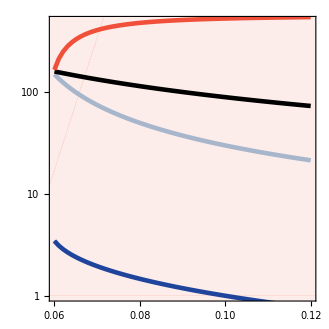

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.06,0.12},{0,6.2}}]
```